# Mean Field solution - seaming two Kitaev materials

## Definitions [Run this!]

```mathematica
Needs["MaTeX`"]
```

```mathematica
Dynamic[Refresh[NotebookSave[];DateString[],UpdateInterval->60]]
```

the Hamiltonian

```mathematica
r[J_]=J;
s[k_,J_]=-2J Cos[k/2];
α[k_,κ_] = 2 κ Sin [k];
β[k_,κ_] =  2 κ Sin [k/2];
γ[h_] = -h;
```

```mathematica
HZMF[k_,n_, J_,κ_,h_,Jt_,χc_,χb_] := N@Normal@SparseArray[   {
					{i_,i_} -> If[ 1<i<2n+ 4 , If[OddQ[i],-α[k,κ], α[k,κ]] , 0],

					{i_,j_} /;Abs[i-j]==1->   
												If[                     ((i==1)∨(j==1))∨((i==2n+ 4)∨(j==2n+ 4)), 
															If[ ((i==1)∨(i==2n+4)), ⅈ γ[h] , - ⅈ γ[h] ], 
															If[EvenQ[Min[i,j]], -(i-j) ⅈ s[k,J] , -(i-j) ⅈ r[J]] ],

					{i_,j_} /;Abs[i-j]==2-> If[ ((i==1)∨(j==1))∨((i==2n+ 4)∨(j==2n+ 4)), 0,  If[OddQ[i],β[k,κ], -β[k,κ]] ],
					  {1,2n+ 4}->  ⅈ Jt χc ,
						{2,2n+ 3} ->  ⅈ Jt χb,
						{2n+ 4,1} -> - ⅈ Jt χc ,
						{2n+ 3,2} -> - ⅈ Jt χb
},					
	{2n+ 4,2n+ 4}					]
```

the sorting [ first positive and the negative energies ]

```mathematica
MySort[list_] :=If[         EvenQ@Length[list],
					Flatten[{Drop[SortBy[list,First],Length[list]/2],Reverse@Take[SortBy[list,First],Length[list]/2]},1]
                                               ,0];
```

and

```mathematica
ChiC = Compile[  {{L,_Integer}, {n,_Integer},{U,_Complex,3} },  2/L Sum[  Sum[  Im[Conjugate[U⟦k⟧⟦m⟧⟦2⟧]*U⟦k⟧⟦m⟧⟦2n+3⟧  ] , {m,1,n+2}]  , {k,1,L}]  ];
 ChiB = Compile[  {{L,_Integer}, {n,_Integer},{U,_Complex,3} },  2/L Sum[  Sum[  Im[Conjugate[U⟦k⟧⟦m⟧⟦1⟧]*U⟦k⟧⟦m⟧⟦2n+4⟧  ] , {m,1,n+2}]  , {k,1,L}]  ];
```

```mathematica
parametersMF = Module[{k,m, EV},  
					  EV =  Transpose[#3]⟦2⟧;
					{ ChiC[#1,#2,EV]   , ChiB[#1,#2,EV]   }
] &
```

Module[{k,m,EV},EV=Transpose[#3]⟦2⟧;{ChiC[#1,#2,EV],ChiB[#1,#2,EV]}]&

## More definitions

### Linear Fit from data

what a function that maps a set of data {L=100,L=150,L=200,...} to fitted value expected to L-> \infty

```mathematica
(* this function works, but does not gives the error bar 

finiteSizeCorrectionFit[set_,variable_Integer,Jt_Integer] := Module[ {size=Length[set],data,fit,x},
																data = Table[  {set⟦i,Jt,2⟧^-1 , set⟦i,Jt,variable⟧}, {i,1,size}];
																fit = Fit[ data , {1,x} , x] ;
																fit /. x-> 0
									]
*)
```

```mathematica
finiteSizeCorrectionLinearModel[set_,variable_Integer,Jt_Integer] :=
							 Module[ {size=Length[set],data,lm,x,TableEntries,linearCoeff,linearCoeffSD},
									data = Table[  {set⟦i,Jt,2⟧^-1 , set⟦i,Jt,variable⟧}, {i,1,size}];
									lm = LinearModelFit[data,{1,x},x];
									TableEntries = lm["ParameterTableEntries"];
									linearCoeff = TableEntries⟦1,1⟧;
									linearCoeffSD =  TableEntries⟦1,2⟧;
									Around[ linearCoeff, linearCoeffSD ]
									]
```

```mathematica
finiteSizeCorrectionLinearModel[set,5,2]
```

2.030.3210^-9

the  function finiteSizeCorrectionLinearModel  works for a given value of Jt, I want a function that gives the array { ... { Jt , Δ* } ...} where Δ* is the limit value. The input is just the data.

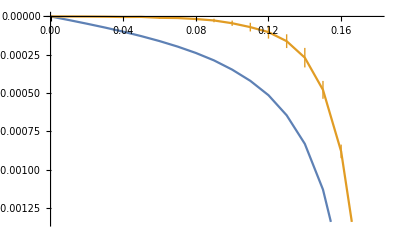

```mathematica
ListPlot[{c,cinf}, Joined->True]
```

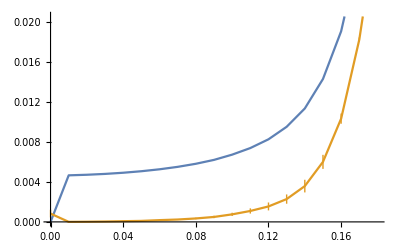

```mathematica
ListPlot[{b,binf}, Joined->True]
```

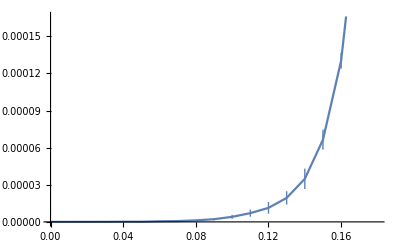

```mathematica
ListPlot[ gapinf , Joined->True]
```

```mathematica
gapinf = finiteSizeCorrectionGap[set]
```

{{0.,-3.91.910^-16},{0.01,2.030.3210^-9},{0.02,1.290.1310^-8},{0.03,4.720.3210^-8},{0.04,1.320.0610^-7},{0.05,1.40.710^-7},{0.06,5.4.10^-7},{0.07,6.72.410^-7},{0.08,1.20.510^-6},{0.09,2.21.010^-6},{0.1,4.11.610^-6},{0.11,7.12.910^-6},{0.12,0.0000115},{0.13,0.0000195},{0.14,0.0000358},{0.15,0.0000668},{0.16,0.0001307},{0.17,0.000261429},{0.18,0.000487026}}

```mathematica
finiteSizeCorrectionChic[set_]:=
							
							 Module[ {table,size=Length[set],data, Jt,Jf = Min[Length/@ set]},
									table={};
									For[ Jt = 1 , Jt ≤ Jf , Jt++,
										AppendTo[table, {set⟦1,Jt,1⟧,finiteSizeCorrectionLinearModel[set,3,Jt]}]
									];
									table
									]
```

```mathematica
finiteSizeCorrectionChib[set_]:=
							
							 Module[ {table,size=Length[set],data, Jt,Jf = Min[Length/@ set]},
									table={};
									For[ Jt = 1 , Jt ≤ Jf , Jt++,
										AppendTo[table, {set⟦1,Jt,1⟧,finiteSizeCorrectionLinearModel[set,4,Jt]}]
									];
									table
									]
```

```mathematica
finiteSizeCorrectionGap[set_]:=
							
							 Module[ {table,size=Length[set],data, Jt,Jf = Min[Length/@ set]},
									table={};
									For[ Jt = 1 , Jt ≤ Jf , Jt++,
										AppendTo[table, {set⟦1,Jt,1⟧,finiteSizeCorrectionLinearModel[set,5,Jt]}]
									];
									table
									]
```

#### ideas & drafts for -- finiteSizeCorrectionFit

```mathematica
fN =FileNameJoin[{NotebookDirectory[], "with-gap",  "4-0.-0.01-0.29-L=100.txt"     }];
	f = OpenRead[fN];
	data0= ReadList[ f];
	Close[f];
fN =FileNameJoin[{NotebookDirectory[], "with-gap",  "4-0.-0.01-0.29-L=150.txt"     }];
	f = OpenRead[fN];
	data1= ReadList[ f];
	Close[f];
fN =FileNameJoin[{NotebookDirectory[], "with-gap",  "4-0.-0.01-0.29-L=200.txt"     }];
	f = OpenRead[fN];
	data2= ReadList[ f];                                                                                                                       Close[f];
```

```mathematica
set = {data0,data1,data2};
```

```mathematica
(*
p = Predict[{N@100^-1 -> 3.6026848016978457 10^-16,  N@150^-1 ->  2.2653928174623126 10^-17, N@200^-1 ->  2.265350465815473 10^-17} , Method->"LinearRegression" ]
*)
```

```mathematica
StandardDeviation[p[0,"Distribution"]]
```

2.1964×10^-16

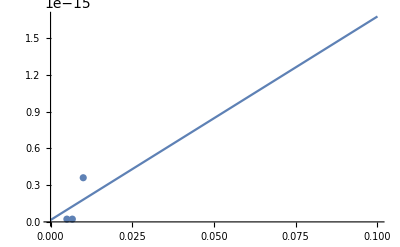

```mathematica
Show[Plot[p[x], {x,0,.1}], ListPlot[{{100^-1,3.6026848016978457*^-16},{150^-1,2.2653928174623126*^-17},{200^-1,2.265350465815473*^-17}}]]
```

```mathematica
data = Table[  {set⟦i,1,2⟧ , set⟦i,1,5⟧}, {i,1,3}]
```

{{100,3.60268×10^-16},{150,2.26539×10^-17},{200,2.26535×10^-17}}

testing the first funciton

```mathematica
finiteSizeCorrection[  {data1,data2},5,1]
```

2.26522×10^-17

```mathematica
lm = LinearModelFit[ data , {1,x} , x ]
```

FittedModel[6.41614×10^-16-3.37615×10^-18 x]

```mathematica
lm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
StandardDeviation[lm]
```

StandardDeviation[FittedModel[6.41614×10^-16-3.37615×10^-18 x]]

```mathematica
tab = lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 6.41614×10^-16 | 3.03018×10^-16 | 2.11741 | 0.280891
x | -3.37615×10^-18 | 1.94922×10^-18 | -1.73206 | 0.333333

```mathematica
te = lm["ParameterTableEntries"]
```

{{6.41614×10^-16,3.03018×10^-16,2.11741,0.280891},{-3.37615×10^-18,1.94922×10^-18,-1.73206,0.333333}}

```mathematica
Around[ te[[1,1]], te[[1,2]]]
```

6.43.010^-16

```mathematica
lm["ParameterErrors"]
```

{3.03018×10^-16,1.94922×10^-18}

```mathematica
tab["Estimate"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 6.41614×10^-16 | 3.03018×10^-16 | 2.11741 | 0.280891
x | -3.37615×10^-18 | 1.94922×10^-18 | -1.73206 | 0.333333[Estimate]

#### Hamiltonian for some fixed lengths -- [DRAFT]

for L = 100 , 200 , 300, 400 and 500

```mathematica
(*
H100 = Compile[ {{k,_Real}, {J,_Complex},{κ,_Real},{hz,_Real},{Jt,_Complex}, {χc,_Real}, {χb,_Real} } ,
SparseArray[   {
					{i_,i_} -> If[ 1<i<104 , If[OddQ[i],-2 κ Sin [k],2 κ Sin [k]] , 0],

					{i_,j_} /;Abs[i-j]==1->   
												If[                     ((i==1)∨(j==1))∨((i==104)∨(j==104)), 
															If[ ((i==1)∨(i==104)), -ⅈ hz ,  ⅈ hz ], 
															If[EvenQ[Min[i,j]], (i-j) ⅈ 2J Cos[k/2], -(i-j) ⅈ J] ],

					{i_,j_} /;Abs[i-j]==2-> If[ ((i==1)∨(j==1))∨((i==104)∨(j==104)), 0,  If[OddQ[i],2 κ Sin [k/2], -2 κ Sin [k/2]] ],
					  {1,104}->  ⅈ Jt χc ,
						{2,2n+ 3} ->  ⅈ Jt χb,
						{2n+ 4,1} -> - ⅈ Jt χc ,
						{2n+ 3,2} -> - ⅈ Jt χb
},					
	{104,104}					],RuntimeAttributes->{Listable}   ]
*)
```

```mathematica
(*
H200 = Function[ {k,J,κ,hz,Jt,χc,χb } ,

Table[(-1)^(i-1)2 κ Sin [k]Sign[i]Sign[L+1-i] KroneckerDelta[i,j]+Sign[i]Sign[L-i]I ((J-2.Cos[k/2])/2+(-1)^i(J+2.Cos[k/2])/2)  KroneckerDelta[i+1,j]-Sign[j]Sign[L-j]I ((J-2.Cos[k/2])/2+(-1)^i(J+2.Cos[k/2])/2)    KroneckerDelta[i-1,j]-I hz KroneckerDelta[1,j]KroneckerDelta[i,0]+I hz KroneckerDelta[1,i]KroneckerDelta[j,0]+I  hz KroneckerDelta[L+1,j]KroneckerDelta[i,L]-I hz KroneckerDelta[L+1,i]KroneckerDelta[j,L]+(-1)^i 2.κ Sin[k/2] Sign[i] Sign[L-i-1]KroneckerDelta[i+2,j]+(-1)^i 2.κ Sin[k/2]  Sign[j]Sign[L-j-1]KroneckerDelta[i,j+2],{i,0,L+1},{j,0,L+1}] ];
*)
```

```mathematica
(* 
ES200 =   Function[ {J,κ,hz,Jt,χc,χb } ,
   Table[  {k,Transpose[Chop@MySort@Transpose@Eigensystem[N@H200 [k,J,κ,hz,Jt,χc,χb ]]] } , {k,0,N[π] , N[π/200]}] 
]
*)
```

```mathematica
(*ES200[0., J,κ,hz,Jt,χc,χb]*)
```

#### tentative for parameter map

and

```mathematica
(*
H = N@ Normal@SparseArray[   {
					{i_,i_} -> If[ 1<i<2n+ 4 , If[OddQ[i],-2 κ Sin [k],2 κ Sin [k]] , 0],

					{i_,j_} /;Abs[i-j]==1->   
												If[                     ((i==1)∨(j==1))∨((i==2n+ 4)∨(j==2n+ 4)), 
															If[ ((i==1)∨(i==2n+4)), -ⅈ hz ,  ⅈ hz ], 
															If[EvenQ[Min[i,j]], (i-j) ⅈ 2J Cos[k/2], -(i-j) ⅈ J] ],

					{i_,j_} /;Abs[i-j]==2-> If[ ((i==1)∨(j==1))∨((i==2n+ 4)∨(j==2n+ 4)), 0,  If[OddQ[i],2 κ Sin [k/2], -2 κ Sin [k/2]] ],
					  {1,2n+ 4}->  ⅈ Jt χc ,
						{2,2n+ 3} ->  ⅈ Jt χb,
						{2n+ 4,1} -> - ⅈ Jt χc ,
						{2n+ 3,2} -> - ⅈ Jt χb
},					
	{2n+ 4,2n+ 4}					] ;
*)
```

```mathematica
(*parametersMF = Compile[ {{Lx,_Integer},{n,_Integer}, {J,_Real},{κ,_Real},{hz,_Real},{Jt,_Real}, {χc,_Real}, {χb,_Real} } , 

EV =  Table[  {k, Transpose[Chop@MySort@Transpose@Quiet@Eigensystem[N@HZMF[k,n, J,κ,hz,Jt,χc,χb ] ]]⟦2⟧   } , {k,0,π , π/Lx}];
							{2/Lx Sum[  Sum[  Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦2⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2n+3⟧
						] , {m,1,n+2}]  , {k,1,Lx}]  , 2/Lx Sum[  Sum[ Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦1⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2n+4⟧  ] , {m,1,n+2}]
						 , {k,1,Lx}]  }
] *)
```

```mathematica
(*
parametersMF = FunctionCompile@ Function[Module[{k,m},  EV =  Table[  {k, Transpose[Chop@MySort@Transpose@Quiet@Eigensystem[N@HZMF[k,#2, #3,#4,#5,#6,#7,#8 ] ]]⟦2⟧   } , {k,0,π , π/#1}];
							{2/#1 Sum[  Sum[  Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦2⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2#2+3⟧
						] , {m,1,#2+2}]  , {k,1,#1}]  , 2/#1 Sum[  Sum[ Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦1⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2#2+4⟧  ] , {m,1,#2+2}]
						 , {k,1,#1}]  }
] ]
*)
```

```mathematica
(*
Timing[parametersMF [L,n, J,κ,hz,Jt,χc,χb]]
*)
```

#### χc and χb

```mathematica
Clear[n]
```

```mathematica
parametersMF = Module[{k,m},  
					  EV =  Transpose[ ]⟦2⟧;
					{ ChiC[#1,#2,EV]   , ChiB[#1,#2,EV]   }
] &
```

Module[{k,m},EV=Transpose[Table[{k,Transpose[Chop[MySort[Transpose[Quiet[Eigensystem[N[HZMF[k,#2,#3,#4,#5,#6,#7,#8]]]]]]]]⟦2⟧},{k,0,π,π/#1}]]⟦2⟧;{ChiC[#1,#2,EV],ChiB[#1,#2,EV]}]&

```mathematica
Timing[parametersMF [L,n, J,κ,hz,Jt,χc,χb]]
```

{2.45313,{-1.47257×10^-13,-0.0115708}}

```mathematica
EV =  Transpose[Table[  {k, Transpose[Chop@MySort@Transpose@Quiet@Eigensystem[N@HZMF[k,#2, #3,#4,#5,#6,#7,#8 ] ]]⟦2⟧   } , {k,0,π , π/#1}]&[L,n, J,κ,hz,Jt,χc,χb]]⟦2⟧;
```

```mathematica
Transpose[EV][[2]][[1]][[2]]
```

{0.-0.0966665 ⅈ,0.230497,0.+0.111141 ⅈ,-0.330941,0.-0.249199 ⅈ,0.370277,0.+0.341243 ⅈ,-0.341243,0.-0.370277 ⅈ,0.249199,0.+0.330941 ⅈ,-0.111141,0.-0.230497 ⅈ,-0.0966665}

### Create files [ ignore ]

I want to store the data in a “.txt” file in the structure ( L , jt , χc , χb )

```mathematica
fN = "C:\\Users\\lucas\\Desktop\\lucas\\Wolfram Mathematica\\Wolfram Mathematica\\Master-definitive\\data\\l_25.txt";
f = OpenWrite[fN];
Write[ f , {0,0,0}];
Close[f];
```

```mathematica
(*file2 = OpenRead[file2Name];
v = Read[ OpenRead[file2Name]];*)
```

the files are named according to the Lx = Ly size.

### Self consistent solution (main code) [ change the Lx and Ly -- 2+hours for L>100 ]

```mathematica
J=1;
{hx,hy,hz}=0.85/√3{1,1,1};
κ = hx*hy*hz;

steps=80;
deltaJt=0.02;
acuracy = 4;
```

I will allocate the  points { J̃, χ } in matrix “b” and “c”, for this I initialize two empty matrices and at the end of each loop  I append output of each loop to the matrix.

#### code

```mathematica
For[ L=100, L ≤ 300 , L=L+100,
	Lx=L; n=Floor[L/2]-2;
...

]
```

```mathematica
(*t0 = AbsoluteTime[];*)
b = {};
c = {};
j0 =0.01;
jf  =0.8;
For[jt=j0,jt<jf,jt=jt+deltaJt,
	chib = Table[0,steps];
	chib⟦1⟧= If[jt==j0,0.01,0.01+ 1.005b⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧ ];
	chic = Table[0,steps];
	chic⟦1⟧ =   If[jt==j0,-0.005, -0.005+ 1.005 c⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧ ];
	Δa=1;
	Δb=1;
	(*Δc=1;*)
	For[i=1,(( i<steps)∧( (Δa≠ 0)∨(Δb≠0)) )  , i++,											
	EV =  Table[  {k, Transpose[Chop@MySort@Transpose@Quiet@Eigensystem[N@HZMF[k,n, J,κ,hz,jt,chic⟦i⟧,chib⟦i⟧ ] ]]⟦2⟧   } , {k,0,π , π/Lx}];
							chic⟦i+1⟧=2/Lx Sum[  Sum[  Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦2⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2n+3⟧
						] , {m,1,n+2}]  , {k,1,Lx}] ;
							chib⟦i+1⟧=2/Lx Sum[  Sum[ Im[Conjugate[EV⟦k⟧⟦2⟧⟦m⟧⟦1⟧]*EV⟦k⟧⟦2⟧⟦m⟧⟦2n+4⟧  ] , {m,1,n+2}]
						 , {k,1,Lx}]  ;
(* Print[chic[[i+1]] "c="];*)
Δa = Chop[Abs[Abs@chib⟦i+1⟧-Abs@ chib⟦i⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i+1⟧-Abs@ chic⟦i⟧ ], 10^-acuracy ];
Δb = If[i==1,1.0 ,Chop[Abs[Abs@chib⟦i⟧-Abs@ chib⟦i-1⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i⟧-Abs@ chic⟦i-1⟧ ], 10^-acuracy ]]
(*Δc = If[i≤ 2,1.0 ,Chop[Abs[Abs@chib⟦i-1⟧-Abs@ chib⟦i-2⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i-1⟧-Abs@ chic⟦i-2⟧ ], 10^-acuracy ]];*)
(*Print[Δa"deltaA="];
Print[Δc"deltaC="];*)
		];(*Print["χb="Last[chib]]; Print["χc="Last[chic]];*)
	(*t=AbsoluteTime[];*)
	(*Print["Jt = ",jt , ";  Max Step: i=",i , ";  Timing = ",  Floor[(t-t0)/3600], "h ",Floor[(t-t0)/60-60*Floor[(t-t0)/3600]], "m"];*)
	AppendTo[ b , {jt , chib⟦i⟧ } ];
	 AppendTo[ c , {jt ,chic⟦i⟧} ] ;
	f = OpenAppend[fN];
	Write[ f, {jt ,chic⟦i⟧,chib⟦i⟧}];
	Close[f];
 ]
```

#### Plot

```mathematica
lineJt = Line[ {{0.08,-1.5},{0.08,2.0}}];
```

```mathematica
bPlot = ListPlot[ b, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_b",Magnification->2] } , PlotRange-> {0,1},Joined->False, PlotMarkers->{"●"},Frame->True,PlotStyle->{Darker[Blue]},   FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\ell_x=\\ell_y=200",Magnification->1.8] ,20 ,Black ] (*, Epilog-> {Directive[Thin,Black,Dashed],lineJt}*)]
```

-Graphics-

```mathematica
cPlot=ListPlot[ c, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_c",Magnification->2] }  ,   PlotRange-> {-1.5/2,0},Joined->False,PlotMarkers->{"●"},Frame->True,PlotStyle->{Darker[Red]}, Frame->True,  FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\ell_x=\\ell_y=200",Magnification->1.8] ,20 ,Black ] (*, Epilog-> {Directive[Thin,Black,Dashed],lineJt}*)]
```

-Graphics-

### Self consistent solution (alternative code) [ ]

```mathematica
J=1;
{hx,hy,hz}=0.85/√3{1,1,1};
κ = hx*hy*hz;
steps=30;
deltaJt=0.01;
j0 =0.0; jf  =0.29;
acuracy = 4;
```

I will allocate the  points { J̃, χ } in matrix “b” and “c”, for this I initialize two empty matrices and at the end of each loop  I append output of each loop to the matrix.

#### code

```mathematica
(*
For[ L=100, L ≤ 350 , L=L+50,
		path = FileNameJoin[{       NotebookDirectory[]    , "with-gap",     StringReplace["a-j0-dj-jf-L=X.txt",{"X"-> ToString[L],"j0"-> ToString[j0],"dj"-> ToString[deltaJt],"jf"-> ToString[jf] , "a"-> ToString[acuracy]}]    }];
		f = OpenWrite[path];
		(*Write[f,{"hello"}];*)
		Close[f];
]
```

```mathematica
t0 = AbsoluteTime[] ;
For[ L=100, L ≤ 200 , L=L+100,
	Lx=L; n=Floor[L/2]-2;
	b = {}; c = {}; 
	
	fN =FileNameJoin[{NotebookDirectory[],  StringReplace["4-0.01-0.01-0.29-L=X.txt",{"X"-> ToString[L]}]     }];
	f = OpenRead[fN];
	cb = ReadList[ f];
	Close[f];
	
	For[jt=0.19,jt<jf,jt=jt+deltaJt,
		Module[ {chib = Table[0,steps], chic = Table[0,steps], i},
		                  chib⟦1⟧=If[jt ≤ j0   , 0 ,0.4 cb⟦Round[(jt-j0)/deltaJt]⟧⟦4⟧ + 0.6b⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧ ];    	(* If[jt ≤ j0   ,0.005, 0.0001+ 1.005b⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧* ];  *) 
		                  chic⟦1⟧ = If[jt ≤ j0   ,0 ,0.4 cb⟦Round[(jt-j0)/deltaJt]⟧⟦3⟧ + 0.6c⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧ ];    	(* If[jt≤ j0,-0.0003,-0.0005+ 1.005 c⟦Round[(jt-j0)/deltaJt]⟧⟦2⟧ ];*)
				Δa=1;						 Δb=1;
		                   For[i=1,(( i<steps)∧( (Δa≠ 0)∨(Δb≠0)) )  , i++,
			                 ES=  Table[  {k, Transpose[Chop@MySort@Transpose@Eigensystem[HZMF[k,n, J,κ,hz,jt,chic⟦i⟧,chib⟦i⟧ ]]]⟦2⟧   } , {k,0,N[π] , N[π/L]}];
			                 {chic⟦i+1⟧,chib⟦i+1⟧ } = parametersMF[L,n, ES ];                      
			                   Δa = Chop[Abs[Abs@chib⟦i+1⟧-Abs@ chib⟦i⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i+1⟧-Abs@ chic⟦i⟧ ], 10^-acuracy ];
			                   Δb = If[i ≤ 2,1.0 ,Chop[Abs[Abs@chib⟦i⟧-Abs@ chib⟦i-1⟧ ], 10^-acuracy]+Chop[Abs[ Abs@chic⟦i⟧-Abs@ chic⟦i-1⟧ ], 10^-acuracy ]]
		                          ];
		         AppendTo[ b , {jt , chib⟦i⟧ } ]; 		AppendTo[ c , {jt ,chic⟦i⟧} ] ;
			gap =  Min@Abs@Eigenvalues@HZMF[0,n, J,κ,hz,jt,chic⟦i⟧,chib⟦i⟧ ];

			Δt =  UnitConvert[ Quantity[AbsoluteTime[] -t0, "Seconds" ], "Hours" ]; Print["L = ", L , ", jt = ", jt , ", Max Step = ", i , "; Δt = ",  IntegerPart[Δt] ,  IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ] ] ;
		        path = FileNameJoin[{       NotebookDirectory[]    ,  "with-gap",    StringReplace["a-j0-dj-jf-L=X.txt",{"X"-> ToString[L],"j0"-> ToString[j0],"dj"-> ToString[deltaJt],"jf"-> ToString[jf] , "a"-> ToString[acuracy]}]    }];
		        f = OpenAppend[path];
		        Write[ f, {jt , L , chic⟦i⟧,chib⟦i⟧, gap}];
		        Close[f];
		  ]
         ]
]
```

L = 150, jt = 0., Max Step = 4; Δt = 0 h2 min

L = 150, jt = 0.01, Max Step = 4; Δt = 0 h5 min

L = 150, jt = 0.02, Max Step = 4; Δt = 0 h8 min

L = 150, jt = 0.03, Max Step = 4; Δt = 0 h10 min

L = 150, jt = 0.04, Max Step = 4; Δt = 0 h13 min

L = 150, jt = 0.05, Max Step = 4; Δt = 0 h16 min

L = 150, jt = 0.06, Max Step = 4; Δt = 0 h18 min

L = 150, jt = 0.07, Max Step = 6; Δt = 0 h22 min

L = 150, jt = 0.08, Max Step = 6; Δt = 0 h27 min

L = 150, jt = 0.09, Max Step = 6; Δt = 0 h31 min

L = 150, jt = 0.1, Max Step = 6; Δt = 0 h35 min

L = 150, jt = 0.11, Max Step = 6; Δt = 0 h39 min

L = 150, jt = 0.12, Max Step = 6; Δt = 0 h43 min

L = 150, jt = 0.13, Max Step = 8; Δt = 0 h49 min

L = 150, jt = 0.14, Max Step = 8; Δt = 0 h54 min

L = 150, jt = 0.15, Max Step = 7; Δt = 0 h58 min

L = 150, jt = 0.16, Max Step = 9; Δt = 1 h3 min

L = 150, jt = 0.17, Max Step = 13; Δt = 1 h11 min

L = 150, jt = 0.18, Max Step = 17; Δt = 1 h21 min

L = 150, jt = 0.19, Max Step = 19; Δt = 1 h32 min

L = 150, jt = 0.2, Max Step = 21; Δt = 1 h45 min

L = 150, jt = 0.21, Max Step = 15; Δt = 1 h54 min

L = 150, jt = 0.22, Max Step = 17; Δt = 2 h4 min

L = 150, jt = 0.23, Max Step = 17; Δt = 2 h14 min

L = 150, jt = 0.24, Max Step = 17; Δt = 2 h24 min

L = 150, jt = 0.25, Max Step = 17; Δt = 2 h34 min

L = 150, jt = 0.26, Max Step = 16; Δt = 2 h44 min

L = 150, jt = 0.27, Max Step = 16; Δt = 2 h53 min

L = 150, jt = 0.28, Max Step = 15; Δt = 3 h3 min

L = 200, jt = 0., Max Step = 4; Δt = 3 h7 min

L = 200, jt = 0.01, Max Step = 4; Δt = 3 h11 min

L = 200, jt = 0.02, Max Step = 4; Δt = 3 h15 min

L = 200, jt = 0.03, Max Step = 4; Δt = 3 h19 min

L = 200, jt = 0.04, Max Step = 4; Δt = 3 h23 min

L = 200, jt = 0.05, Max Step = 4; Δt = 3 h27 min

L = 200, jt = 0.06, Max Step = 4; Δt = 3 h31 min

L = 200, jt = 0.07, Max Step = 4; Δt = 3 h35 min

L = 200, jt = 0.08, Max Step = 4; Δt = 3 h39 min

L = 200, jt = 0.09, Max Step = 4; Δt = 3 h43 min

L = 200, jt = 0.1, Max Step = 5; Δt = 3 h50 min

L = 200, jt = 0.11, Max Step = 5; Δt = 3 h55 min

L = 200, jt = 0.12, Max Step = 5; Δt = 4 h1 min

L = 200, jt = 0.13, Max Step = 6; Δt = 4 h7 min

L = 200, jt = 0.14, Max Step = 7; Δt = 4 h16 min

L = 200, jt = 0.15, Max Step = 10; Δt = 4 h28 min

L = 200, jt = 0.16, Max Step = 13; Δt = 4 h44 min

L = 200, jt = 0.17, Max Step = 18; Δt = 5 h8 min

L = 200, jt = 0.18, Max Step = 21; Δt = 5 h34 min

$Aborted

#### Plot

```mathematica
lineJt = Line[ {{0.08,-1.5},{0.08,2.0}}];
```

```mathematica
bPlot = ListPlot[ b, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_b",Magnification->2] } , PlotRange-> {0,1},Joined->False, PlotMarkers->{"●"},Frame->True,PlotStyle->{Darker[Blue]},   FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\ell_x=\\ell_y=200",Magnification->1.8] ,20 ,Black ] (*, Epilog-> {Directive[Thin,Black,Dashed],lineJt}*)]
```

-Graphics-

```mathematica
cPlot=ListPlot[ c, FrameLabel-> { MaTeX["\\tilde{J}",Magnification->2] ,  MaTeX["\\chi_c",Magnification->2] }  ,   PlotRange-> {-1.5/2,0},Joined->False,PlotMarkers->{"●"},Frame->True,PlotStyle->{Darker[Red]}, Frame->True,  FrameStyle->Directive[Black,16],ImageSize->500 ,  PlotLabel-> Style[MaTeX["\\ell_x=\\ell_y=200",Magnification->1.8] ,20 ,Black ] (*, Epilog-> {Directive[Thin,Black,Dashed],lineJt}*)]
```

-Graphics-